```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Integrate[ChebyshevT[deg,2x-1],x]
```

1/4 (-ChebyshevT[-1+deg,-1+2 x]/(-1+deg)+ChebyshevT[1+deg,-1+2 x]/(1+deg))

```mathematica
IntCheb[deg_,x_]:=If[deg==1,-x+x^2,1/4 (-ChebyshevT[-1+deg,-1+2 x]/(-1+deg)+ChebyshevT[1+deg,-1+2 x]/(1+deg))];
NIntCheb[deg_,min_,max_]:=N[IntCheb[deg,Min[max,1]]]-N[IntCheb[deg,Max[min,0]]];
MatBase[n_]:=Table[If[Mod[j+k,2]==0,1/(1-(j-k)^2),0],{j,0,n-1},{k,0,n-1}];
MatWc[n_,min_,max_]:=Module[{v},
v=Table[NIntCheb[deg,min,max],{deg,0,n-1}];
Table[v[[Abs[j-k]+1]],{j,0,n-1},{k,0,n-1}]
];
```

## For different N and δ=3/N, draw r(y)~y

```mathematica
Ls={64,256,1024};
ys=Range[99]/100;
dataREps=Table[1-Eigenvalues[N@{
MatWc[L,y-3/L,y+3/L],
MatBase[L]
},1][[1]]
,{L,Ls}
,{y,ys}
];
```

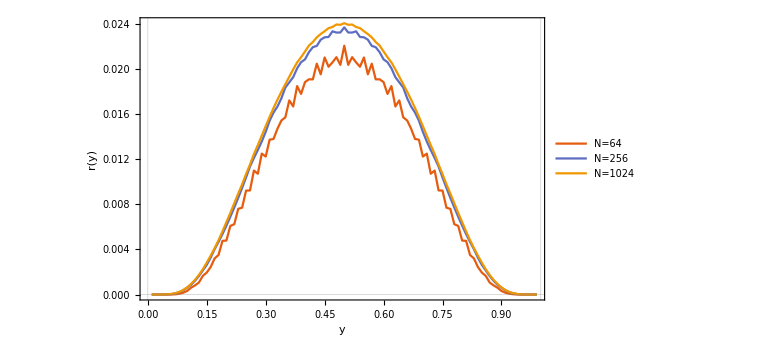

```mathematica
plotREps=ListLinePlot[Map[Transpose[{ys,#}]&,dataREps],
PlotLegends->Placed[
PointLegend[Table[StringForm["N=`1`",L],{L,Ls}],
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendLayout->{"Column",1}],
Scaled[{0.5,0.25}]],
PlotStyle->Automatic,
LabelStyle->Directive[FontSize->20,FontFamily->"Times",Black],
ImageSize->Large,
Frame->True,
FrameLabel->{{"r(y)",None},{"y",None}},FrameStyle->Directive[FontSize->20,FontFamily->"Times",Black],
PlotStyle->Thick,
PlotTheme->"Scientific",
GridLines->{{0,1},{0}}
]
```

## For different N, draw (δ̃)_ϵ~N ϵ

```mathematica
Clear[getRY];
getRY[L_,eps_,y_]:=getRY[L,eps,y]=1-Eigenvalues[N@{MatWc[L,y-eps/L,y+eps/L],MatBase[L]},1][[1]];
getFiniteDeltaBound[L_,eps_]:=Sum[getRY[L,eps,y],{y,0.025,0.475,0.05}]/10/(1+getRY[L,eps,0.5]);
```

```mathematica
Ls={64,256,1024};
ds=Range[1,5,0.2];
dataDeltaEpsBound=Table[getFiniteDeltaBound[L,d]
,{L,Ls}
,{d,ds}
];
```

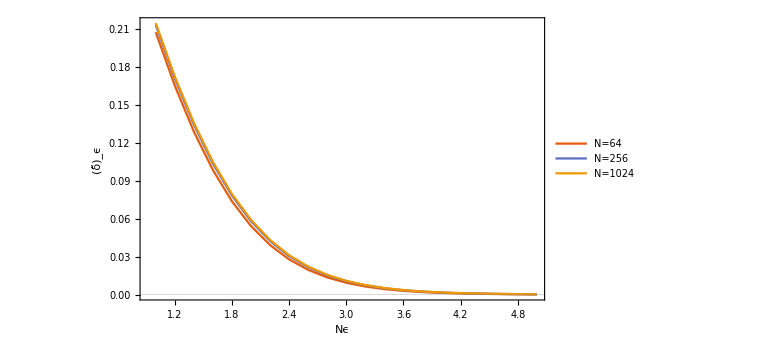

```mathematica
plotDeltaEpsBound=ListLinePlot[Map[Transpose[{ds,#}]&,dataDeltaEpsBound],
PlotLegends->Placed[
PointLegend[Table[StringForm["N=`1`",L],{L,Ls}],
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendLayout->{"Column",1}],
Scaled[{0.85,0.8}]],
PlotStyle->Automatic,
LabelStyle->Directive[FontSize->20,FontFamily->"Times",Black],
ImageSize->Large,
Frame->True,
FrameLabel->{{"(δ̃)_ϵ",None},{"Nϵ",None}},FrameStyle->Directive[FontSize->20,FontFamily->"Times",Black],
PlotStyle->Thick,
PlotRange->Full,
PlotTheme->"Scientific",
GridLines->{{},{0}}
]
```

## Comparison of bound, QPE(sine) and ChebPE

```mathematica
Clear[getDeltaLowerBound,getDeltaQpeSin,getDeltaQpeUnf];
getDeltaLowerBound[eps_]:=getDeltaLowerBound[eps]=getFiniteDeltaBound[256,eps];
getDeltaQpeSin[eps_,n_]:=getDeltaQpeSin[eps,n]=1-Sum[
2/(n(n+1))NIntegrate[
((Sin[π/(n+1)]Cos[1/2(n+1)th])/(2Sin[1/2(th+π/(n+1))] Sin[1/2(th-π/(n+1))]))^2/.th->(ArcCos[2x-1]-(2Pi k)/n)
,{x,Max[Cos[(Pi k)/n]^2-eps/n,0],Min[Cos[(Pi k)/n]^2+eps/n,1]}
,PrecisionGoal->4]
,{k,0,n-1}];
```

```mathematica
epss=Range[1,5,0.2];
dataDelta=Join[Transpose[Table[{
getDeltaLowerBound[eps],
getDeltaQpeSin[eps,256]
},{eps,epss}]],
{Flatten[Import["chebpe.txt","Table"]]}
]
```

{{0.212826,0.170688,0.134214,0.103427,0.0781493,0.0579673,0.04228,0.030384,0.0215587,0.0151342,0.010531,0.00727572,0.00499785,0.00341737,0.00232812,0.00158141,0.00107167,0.000724855,0.000489518,0.000330155,0.000222431},{0.384623,0.305603,0.239169,0.184168,0.139383,0.103572,0.0754993,0.053972,0.0378646,0.026143,0.0178794,0.0122639,0.00860817,0.0063443,0.00501941,0.004286,0.00388932,0.0036537,0.00346747,0.00326908,0.00303257},{0.7442,0.6906,0.6455,0.5979,0.5547,0.518,0.4814,0.4463,0.4149,0.3841,0.3569,0.3291,0.3046,0.2808,0.2582,0.239,0.2197,0.2021,0.1852,0.1711,0.1567}}

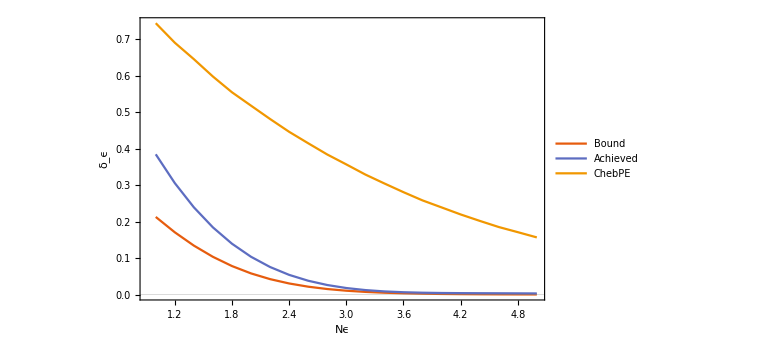

```mathematica
plotDelta=ListLinePlot[Map[Transpose[{epss,#}]&,dataDelta],
PlotLegends->Placed[
PointLegend[{"Bound","Achieved","ChebPE"},
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendLayout->{"Column",1}],
Scaled[{0.85,0.8}]],
PlotStyle->Automatic,
LabelStyle->Directive[FontSize->20,FontFamily->"Times",Black],
ImageSize->Large,
Frame->True,
FrameLabel->{{"δ_ϵ",None},{"Nϵ",None}},FrameStyle->Directive[FontSize->20,FontFamily->"Times",Black],
PlotStyle->Thick,
PlotRange->Full,
PlotTheme->"Scientific",
GridLines->{{},{0}}
]
```

## Search the δ at different ϵ

```mathematica
Import[".\\brent.wl"];
```

```mathematica
findEpsLowerBound[delta_]:=brentmethod[getDeltaLowerBound,delta,1,5,0.001];
{findEpsLowerBound[0.1],findEpsLowerBound[0.05],findEpsLowerBound[0.01]}
```

{1.62569,2.09496,3.0288}

```mathematica
findEpsQpeSin[delta_]:=brentmethod[getDeltaQpeSin[#,256]&,delta,1,5,0.001];
{findEpsQpeSin[0.1],findEpsQpeSin[0.05],findEpsQpeSin[0.01]}
```

{2.02357,2.44446,3.31348}